# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

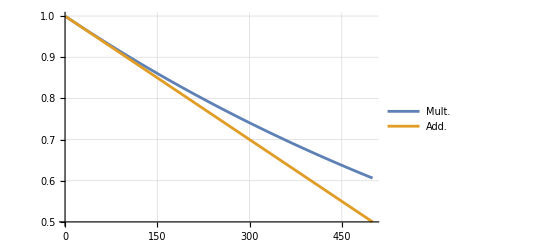

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params1={NN->1000,s->10^-4,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/10000,κ→1,L→2500,u→1/100000}

```mathematica
params2={NN->1000,s->10^-2,κ->1,L->40000,u->10^-5}
```

{NN→1000,s→1/100,κ→1,L→40000,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(40 (1-ⅇ^(-20 B))^3)/((1+ⅇ^(-20 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
bfun02[.02]
```

-3.90882

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-10]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

May need to adjust starting value (2nd argument) if this fails:

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.01]
```

0.0454884

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.522729

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/1000,κ→1,L→10000,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-3.0903 (1-0.976521^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{998.298,45.4903,45.4884,45.4884,45.4884}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Doing it on HRI

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-3.0903 (1-0.976521^(1+τ))^2),998.298,45.4884}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

```mathematica
{{x->0.,y->999.9758849338513},{x->500.,y->341.47926284834415},{x->1000.,y->256.92444267278876},{x->1500.,y->247.3500977052783},{x->2000.,y->246.16752998190728},{x->2500.,y->246.01970478874085},{x->3000.,y->246.0011980558869},{x->3500.,y->245.99888069501498},{x->4000.,y->245.99859051471174},{x->4500.,y->245.99855417817884},{x->5000.,y->245.99854962809712}}
```

{{x→0.,y→999.976},{x→500.,y→341.479},{x→1000.,y→256.924},{x→1500.,y→247.35},{x→2000.,y→246.168},{x→2500.,y→246.02},{x→3000.,y→246.001},{x→3500.,y→245.999},{x→4000.,y→245.999},{x→4500.,y→245.999},{x→5000.,y→245.999}}

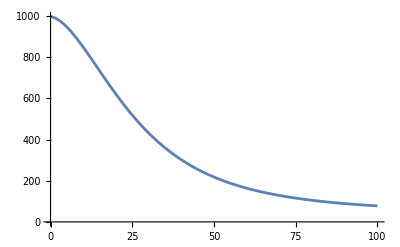

```mathematica
Plot[rAndL⟦1⟧,{τ,0,100}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

{1000 ⅇ^(-3.0903 (1-0.976521^(1+τ))^2),998.298,45.4884}

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→18.2256},{τ→-14.148}}

```mathematica
inv
```

{{τ→-42.0886 Log[6.42406×10^-17 (1.59407×10^16-1. √(2.54107×10^32-8.22275×10^31 Log[0.0219836093160656 y]))]},{τ→-42.0886 Log[6.4240639523306×10^-17 (1.5940749057208×10^16+√(2.5410748050489×10^32-8.2227523314119×10^31 Log[0.0219836093160656 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-42.0886 Log[6.42406×10^-17 (1.59407×10^16-1. √(2.54107×10^32-8.22275×10^31 Log[0.0219836093160656 y]))]

```mathematica
inv2/.y->660//N
```

18.2256

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}

```mathematica
xy1={xs,ys}//N
```

{{0.,14.6332,29.2663,43.8995,58.5327,73.1658,87.799,102.432,117.065,131.699,146.332},{999.363,786.848,594.823,441.552,332.31,257.358,206.178,170.87,146.113,128.443,75.327}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,4.76288,9.71897,13.888,18.012,22.4236,27.4501,33.5864,41.8252,54.8835,87.0064},{998.298,903.017,807.736,712.455,617.174,521.893,426.612,331.331,236.05,140.769,45.4884}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-146.847 0.976521^(1+τ) (1-0.976521^(1+τ)) ⅇ^(-3.0903 (1-0.976521^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

36.3733

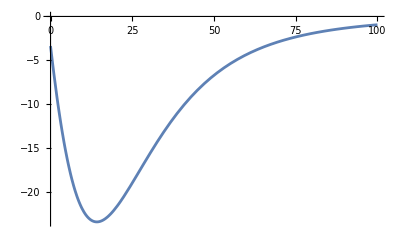

```mathematica
Plot[Nprime01p/.τ->t,{t,0,100}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Part::partd: Part specification xy1⟦1⟧ is longer than depth of object.

Part::partd: Part specification xy1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Piecewise::pairs: The first argument {1.,xy1,{2.,x>1.},{0.,True}} of Piecewise is not a list of pairs.

Piecewise[N[Join[pRules0$7212,{{Last[xy1⟦2⟧],x>Last[xy1⟦1⟧]}},{{0,True}}]]]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{998.298, x<4.76288}, {903.017, x<9.71897}, {807.736, x<13.888}, {712.455, x<18.012}, {617.174, x<22.4236}, {521.893, x<27.4501}, {426.612, x<33.5864}, {331.331, x<41.8252}, {236.05, x<54.8835}, {140.769, x<87.0064}, {45.4884, x>87.0064}, {0., True}}]

Piecewise::pairs: The first argument {1.,xy1,{2.,x>1.},{0.,True}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {1.,xy1,{2.,False},{0.,True}} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

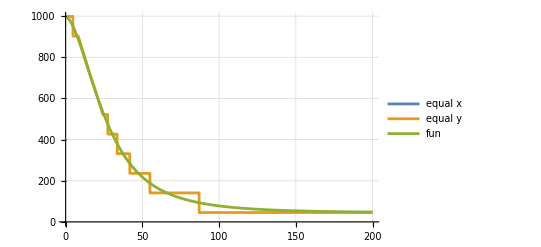

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,200},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

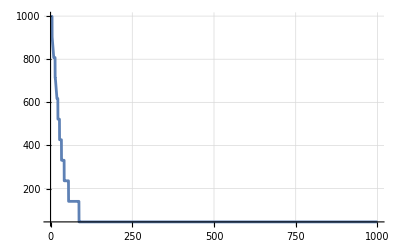

```mathematica
Plot[pwNe2/.x->t,{t,0,1000},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{998.298, x<4.76288}, {903.017, x<9.71897}, {807.736, x<13.888}, {712.455, x<18.012}, {617.174, x<22.4236}, {521.893, x<27.4501}, {426.612, x<33.5864}, {331.331, x<41.8252}, {236.05, x<54.8835}, {140.769, x<87.0064}, {45.4884, x>87.0064}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

166.41

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{0.134127,1.93951×10^-7}

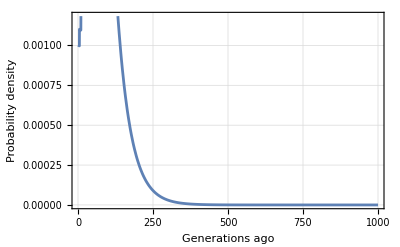

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{10.4047,109.216}

```mathematica
a01[[2]]
```

109.216

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{164.989,0.636733},{140.348,0.154453},{140.084,0.0699955},{139.875,0.0417843},{139.589,0.028946},{139.25,0.0220076},{139.284,0.0178224},{138.942,0.0150855},{138.91,0.0131727}}

```mathematica
Export["v07sfs10.txt", n10All]
```

v07sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{325.149,0.582882},{296.798,0.157231},{296.89,0.0718488},{296.574,0.0419119},{296.399,0.0280071},{296.764,0.0203769},{296.738,0.0157146},{296.799,0.0126479},{296.703,0.0105203},{296.688,0.00898332},{296.583,0.00783666},{296.638,0.00695794},{296.621,0.00626866},{296.519,0.00571654},{296.649,0.00526565},{296.644,0.00489078},{296.702,0.00457384},{296.477,0.00430171},{296.548,0.00406474}}

```mathematica
Export["v07sfs20.txt", n20All]
```

v07sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{656.469,0.531275},{600.807,0.162078},{600.66,0.0771947},{600.74,0.0453981},{600.596,0.0301869},{600.72,0.0217288},{600.661,0.0165227},{600.695,0.0130766},{600.728,0.0106684},{600.675,0.00891394},{600.642,0.00759308},{600.684,0.00657204},{600.589,0.00576548},{600.771,0.00511677},{600.644,0.00458703},{600.499,0.00414878},{600.692,0.00378208},{600.635,0.0034722},{600.79,0.003208},{600.768,0.00298094},{600.857,0.00278435},{600.745,0.002613},{600.557,0.00246268},{600.793,0.00233002},{600.609,0.00221227},{600.723,0.00210718},{600.876,0.00201289},{600.944,0.00192787},{600.734,0.00185082},{600.92,0.00178066},{600.753,0.00171649},{600.738,0.00165754},{600.769,0.00160316},{600.761,0.00155279},{600.842,0.00150596},{600.797,0.00146227},{600.927,0.00142137},{600.671,0.00138297},{600.799,0.0013468}}

```mathematica
Export["v07sfs40.txt", n40All]
```

v07sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1330.39,0.477139},{1226.09,0.164605},{1219.99,0.0833623},{1220.31,0.0504948},{1219.85,0.0340152},{1219.85,0.0245913},{1220.18,0.0186947},{1220.27,0.0147545},{1220.15,0.0119861},{1220.14,0.00996274},{1220.36,0.00843613},{1219.83,0.00725378},{1219.9,0.00631784},{1220.03,0.00556316},{1220.21,0.00494493},{1220.22,0.00443151},{1220.07,0.00400004},{1220.15,0.00363363},{1219.71,0.00331958},{1219.87,0.00304819},{1219.54,0.00281194},{1219.3,0.00260492},{1219.28,0.00242244},{1219.32,0.00226071},{1219.43,0.00211667},{1219.42,0.00198782},{1219.34,0.00187207},{1219.46,0.00176771},{1219.33,0.00167328},{1219.12,0.00158756},{1219.2,0.00150951},{1219.07,0.00143824},{1219.03,0.00137301},{1219.05,0.00131313},{1219.22,0.00125806},{1219.5,0.00120729},{1219.52,0.00116038},{1219.99,0.00111695},{1219.94,0.00107668},{1220.07,0.00103925},{1220.14,0.00100441},{1220.14,0.000971921},{1219.98,0.000941575},{1220.03,0.000913184},{1220.01,0.000886581},{1220.,0.000861613},{1219.65,0.000838146},{1219.99,0.000816057},{1219.82,0.000795234},{1219.89,0.000775577},{1219.61,0.000756996},{1219.34,0.000739407},{1219.45,0.000722736},{1219.27,0.000706912},{1219.36,0.000691875},{1219.46,0.000677567},{1219.41,0.000663935},{1219.56,0.000650933},{1219.31,0.000638515},{1219.3,0.000626642},{1219.61,0.000615277},{1219.4,0.000604387},{1219.42,0.000593939},{1219.56,0.000583906},{1219.45,0.000574261},{1219.18,0.000564979},{1219.15,0.000556039},{1219.06,0.00054742},{1219.13,0.000539102},{1219.07,0.000531068},{1219.25,0.000523301},{1219.3,0.000515787},{1219.37,0.000508512},{1219.24,0.000501462},{1219.31,0.000494625},{1219.24,0.000487991},{1222.21,0.000481549},{1219.16,0.000475289},{1219.33,0.000469203}}

```mathematica
Export["v07sfs80.txt", n80All]
```

v07sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11

#### Comeron 2002 params

Their α is our γ,
their β is Ne×μ with μ=(w+v), i.e. per-nuc. rates to del and back, respectively
Their w is our u, their v is our κu
Their γ is related to our κ:
γ_Com=v/(w+v)=κu/(u+κu)
Thus, κ=γ/(1-γ)
Their defaults are γ=0.45 and β_N=0.01, i.e.

```mathematica
.45/(1-.45)
```

0.818182